Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Scenario B: Low water influx, water_in=250

Define parameters:

```mathematica
u=0.6;
rh=1.0;
rw=0.5;
dh=0.9;dw=0.4;
alpha=0.4;
beta=300;
p=1;
kh=0.1;
kw=0.01;
n=0.1;
a=0.5;
```

Define water recharge rates:

```mathematica
win=750;
ws=alpha*(win-beta);

wt= win-ws;
```

Define system without fire effects

```mathematica
dhdt[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H
```

```mathematica
dwdt[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W
```

Find Fixed points

```mathematica
Simplify[Solve[dhdt[H,W]==0,H]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→386.667-0.6 W}}

```mathematica
p1=Plot[-1.6666666666666667*H+463.33333,{H,0,300}];
```

```mathematica
Simplify[Solve[dwdt[H,W]==0,W]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→245.833-0.833333 H-0.833333 √(106225.-350. H+H^2)},{W→0.833333 (295.-1. H+√(106225.-350. H+H^2))}}

```mathematica
p2=Plot[312.5-1.6666666666666667*H,{H,0,300},PlotStyle->Red];
```

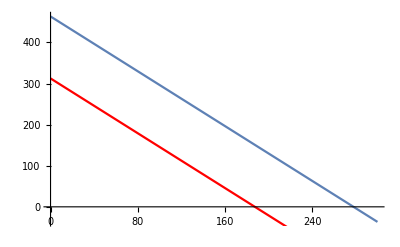

```mathematica
Show[p1,p2]
```

```mathematica
fp=Simplify[Solve[dwdt[H,W]==0 && dhdt[H,W]==0,{H,W}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.,W→312.5},{H→277.778,W→-3.14432×10^-14}}

```mathematica
fp1=Part[fp,1]
```

{H→0.,W→312.5}

```mathematica
fp2=Part[fp,2]
```

{H→277.778,W→-3.14432×10^-14}

Partial Derivatives evaluated at first fixed point: repelling

```mathematica
j11=D[dhdt[H,W],H]/.fp1
```

0.433333

```mathematica
j12=D[dhdt[H,W],W]/.fp1
```

0.

```mathematica
j21=D[dwdt[H,W],H]/.fp1
```

-0.666667

```mathematica
j22=D[dhdt[H,W],W]/.fp1
```

0.

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{0.433333,0.},{-0.666667,0.}}

{0.433333,0.}

{{0.544988,-0.838444},{0.,1.}}

Partial Derivatives evaluated at second fixed point: attracting

```mathematica
j11=D[dhdt[H,W],H]/.fp2
```

-0.9

```mathematica
j12=D[dhdt[H,W],W]/.fp2
```

-0.54

```mathematica
j21=D[dwdt[H,W],H]/.fp2
```

3.05628×10^-17

```mathematica
j22=D[dhdt[H,W],W]/.fp2
```

-0.54

```mathematica
J={{j11,j12},{j21,j22}}
Eigenvalues[J]
Eigenvectors[J]
```

{{-0.9,-0.54},{3.05628×10^-17,-0.54}}

{-0.9,-0.54}

{{1.,0.},{-0.83205,0.5547}}